## k=1, M=1, n=0~3

### convergence of numerical (ok)

```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=1;
mM=1;
nmax=3;
```

```mathematica
prec=200;
```

```mathematica
xmaxnofpointslist={{50,50},{50,100},{50,200},{50,500}};
```

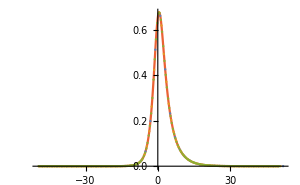
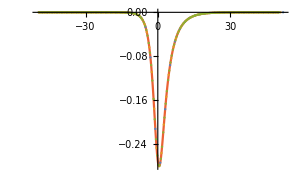
s=1,  n=0
Re
-Graphics-Im
-Graphics-

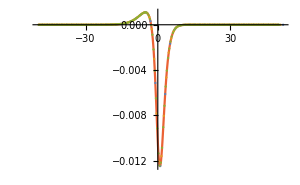
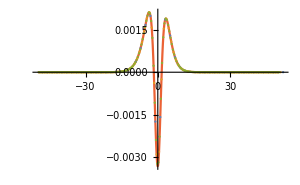
s=1,  n=1
Re
-Graphics-Im
-Graphics-

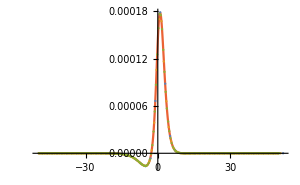
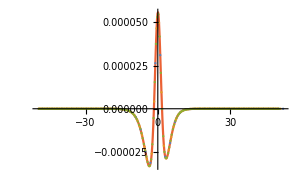
s=1,  n=2
Re
-Graphics-Im
-Graphics-

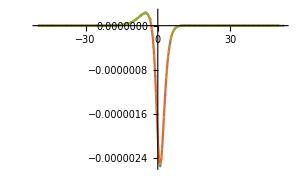
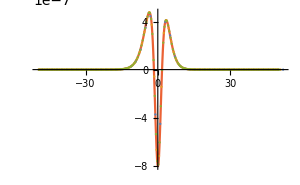
s=1,  n=3
Re
-Graphics-Im
-Graphics-

```mathematica
Table[(
Table[(
Table[(
xmax=xmaxnofpointslist[[a,1]];
nofpoints=xmaxnofpointslist[[a,2]];
(**)
xmin=-xmax;
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[xmin+dx*i,{i,1,nofpoints}];
(**)
hoge=Import[StringJoin["lambda1_numerical/k",ToString[k],"_M",ToString[mM],"/210228_lambda1tilde_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],"_xmax",ToString[xmax],"_nofpoints",ToString[nofpoints],".m"]];
(**)
Reλ1tildenumerical1[a]=Table[{xlist[[i]],Re[hoge[[i]]]},{i,1,nofpoints}];
Imλ1tildenumerical1[a]=Table[{xlist[[i]],Im[hoge[[i]]]},{i,1,nofpoints}];
),{a,1,Length[xmaxnofpointslist]}];
(**)
range=All;
origin=Automatic;
imsize=300;
Print[Column[{
StringJoin["s=",ToString[s],",  n=",ToString[n]],
Row[{Column[{"Re",ListPlot[Table[Reλ1tildenumerical1[a],{a,1,Length[xmaxnofpointslist]}],Joined->Join[ConstantArray[False,Length[xmaxnofpointslist]-1],{True}],PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center],Column[{"Im",ListPlot[Table[Imλ1tildenumerical1[a],{a,1,Length[xmaxnofpointslist]}],Joined->Join[ConstantArray[False,Length[xmaxnofpointslist]-1],{True}],PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center]}]},Center,Frame->True]];
(*
Print["n=",n,"    s=",s,"    ",(Sort[Table[{N[xlist[[i]],3],λ1analytic[[i,2]]/λ1numerical[[i,2]]},{i,1,nofpoints}],Abs[#1[[2]]-1]>Abs[#2[[2]]]&])[[1]]];
*)
),{s,1,mM}];
),{n,0,nmax}];
```

### numerical vs analytic (ok)

```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=1;
mM=1;
nmax=3;
```

```mathematica
xmin=-50;
xmax=50;
nofpoints=500;
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[xmin+dx*i,{i,1,nofpoints}];
prec=200;
```

n=0    s=1    {50.2,1.+0. ⅈ}

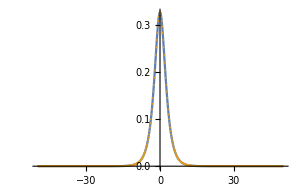
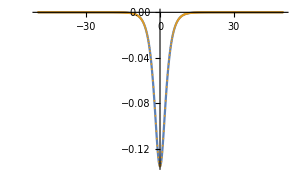
Re
-Graphics-Im
-Graphics-

n=1    s=1    {50.2,0.9965663723937035154139931211994709137477417114053375869626150130782687823325591673939741133429028298543929340347145554251316950862501420775418039980067177571353523482627181207647477666187530936676701+0.000589283008625465885484329384318236287306951172219206344840979166132252530540298791041090108452360440214218376147425434449604329892905265542396453430719264822219954720580166102067935855493592434129 ⅈ}

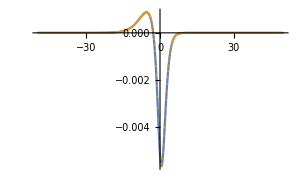
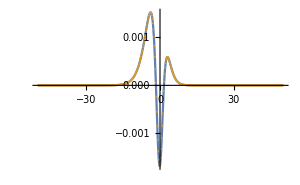
Re
-Graphics-Im
-Graphics-

n=2    s=1    {50.2,0.999999997699444612399471994721375825086461151212419650257981783717304225673967151974027892982312535904984617378036894356647812220558258917038465011162089411333362814018156909994277888804181487181998+1.225976143842084333780691363780307347216043798469828739508223270960069324854522265329644306748666987230892392465856456233686739650625074077499208005404242997955452514242704049884179233904453×10^-9 ⅈ}

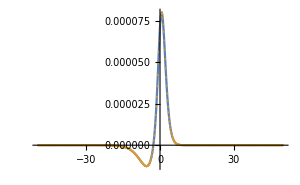
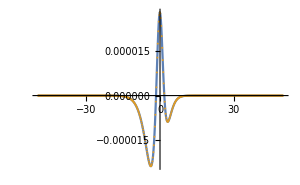
Re
-Graphics-Im
-Graphics-

n=3    s=1    {50.2,0.999999998959539557959043930096502405480509661871502134824140146758927968956120946522233252139378886219619901348762641692276863455114552439455536488747104120040298803867865889644798144481360259922275+5.54265887510066024650802621792652050009010751226682594768376401324913077408191500457513997802894417707686775092448578992471114847066320736875105669294681632766913268888463426349284989303304×10^-10 ⅈ}

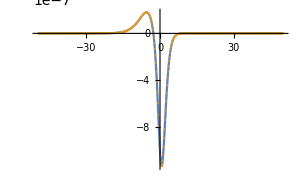
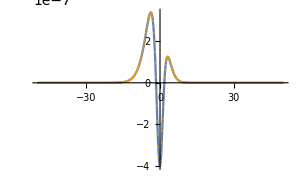
Re
-Graphics-Im
-Graphics-

```mathematica
Table[(
Table[(
hoge=Import[StringJoin["lambda1_analytic/k",ToString[k],"_M",ToString[mM],"/210228_lambda1_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;λ1analytic=Table[{xlist[[i]],N[(hoge/.{u->Exp[xlist[[i]]/(2*k)],logu->xlist[[i]]/(2*k)}),prec]},{i,1,nofpoints}];
Reλ1analytic=Table[{xlist[[i]],Re[λ1analytic[[i,2]]]},{i,1,nofpoints}];
Imλ1analytic=Table[{xlist[[i]],Im[λ1analytic[[i,2]]]},{i,1,nofpoints}];
(**)
hoge=Import[StringJoin["lambda1_numerical/k",ToString[k],"_M",ToString[mM],"/210228_lambda1tilde_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],"_xmax",ToString[xmax],"_nofpoints",ToString[nofpoints],".m"]];
λ1numerical=Table[{xlist[[i]],hoge[[i]]/(1+Exp[xlist[[i]]/(4*k)])},{i,1,nofpoints}];
Reλ1numerical=Table[{xlist[[i]],Re[λ1numerical[[i,2]]]},{i,1,nofpoints}];
Imλ1numerical=Table[{xlist[[i]],Im[λ1numerical[[i,2]]]},{i,1,nofpoints}];
(**)
Print["n=",n,"    s=",s,"    ",(Sort[Table[{N[xlist[[i]],3],λ1analytic[[i,2]]/λ1numerical[[i,2]]},{i,1,nofpoints}],Abs[#1[[2]]-1]>Abs[#2[[2]]]&])[[1]]];
range=All;
origin=Automatic;
imsize=300;
Print[Row[{
Column[{"Re",ListPlot[{Reλ1analytic,Reλ1numerical},Joined->{True,False},PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center],Column[{"Im",ListPlot[{Imλ1analytic,Imλ1numerical},Joined->{True,False},PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center]}]];
),{s,1,mM}];
),{n,0,nmax}];
```

## k=1, M=2, n=0~3

### convergence of numerical (s=2: ok)

```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=1;
mM=2;
nmax=3;
```

```mathematica
prec=200;
```

```mathematica
xmaxnofpointslist={{50,50},{50,100},{50,200},{50,500}};
```

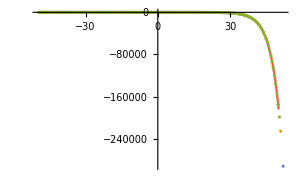
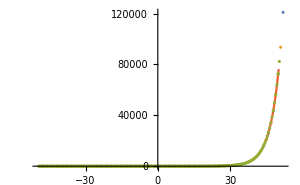
s=1,  n=0
Re
-Graphics-Im
-Graphics-

s=2,  n=0
Re
-Graphics-Im
-Graphics-

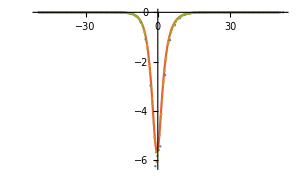
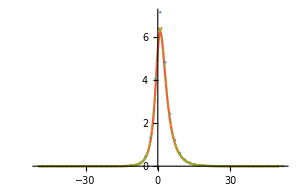
s=1,  n=1
Re
-Graphics-Im
-Graphics-

s=2,  n=1
Re
-Graphics-Im
-Graphics-

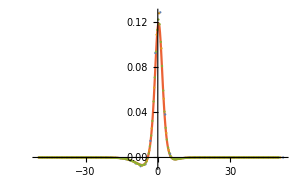
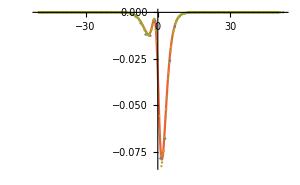
s=1,  n=2
Re
-Graphics-Im
-Graphics-

s=2,  n=2
Re
-Graphics-Im
-Graphics-

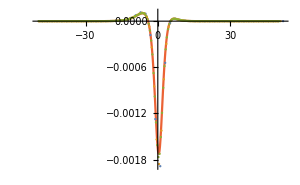
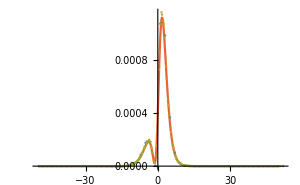
s=1,  n=3
Re
-Graphics-Im
-Graphics-

s=2,  n=3
Re
-Graphics-Im
-Graphics-

```mathematica
Table[(
Table[(
Table[(
xmax=xmaxnofpointslist[[a,1]];
nofpoints=xmaxnofpointslist[[a,2]];
(**)
xmin=-xmax;
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[xmin+dx*i,{i,1,nofpoints}];
(**)
hoge=Import[StringJoin["lambda1_numerical/k",ToString[k],"_M",ToString[mM],"/210228_lambda1tilde_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],"_xmax",ToString[xmax],"_nofpoints",ToString[nofpoints],".m"]];
(**)
Reλ1tildenumerical1[a]=Table[{xlist[[i]],Re[hoge[[i]]]},{i,1,nofpoints}];
Imλ1tildenumerical1[a]=Table[{xlist[[i]],Im[hoge[[i]]]},{i,1,nofpoints}];
),{a,1,Length[xmaxnofpointslist]}];
(**)
range=All;
origin=Automatic;
imsize=300;
Print[Column[{
StringJoin["s=",ToString[s],",  n=",ToString[n]],
Row[{Column[{"Re",ListPlot[Table[Reλ1tildenumerical1[a],{a,1,Length[xmaxnofpointslist]}],Joined->Join[ConstantArray[False,Length[xmaxnofpointslist]-1],{True}],PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center],Column[{"Im",ListPlot[Table[Imλ1tildenumerical1[a],{a,1,Length[xmaxnofpointslist]}],Joined->Join[ConstantArray[False,Length[xmaxnofpointslist]-1],{True}],PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center]}]},Center,Frame->True]];
(*
Print["n=",n,"    s=",s,"    ",(Sort[Table[{N[xlist[[i]],3],λ1analytic[[i,2]]/λ1numerical[[i,2]]},{i,1,nofpoints}],Abs[#1[[2]]-1]>Abs[#2[[2]]]&])[[1]]];
*)
),{s,1,mM}];
),{n,0,nmax}];
```

### numerical vs analytic (s=2: ok) (s=1: not ok (due to non-decaying λ_(s,0,reg) at infinity))

```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=1;
mM=2;
nmax=3;
```

```mathematica
xmin=-50;
xmax=50;
nofpoints=500;
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[xmin+dx*i,{i,1,nofpoints}];
prec=200;
```

n=0    s=1    {50.2,1.+0. ⅈ}

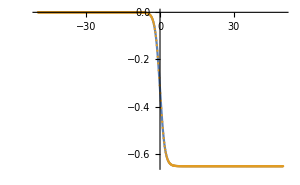
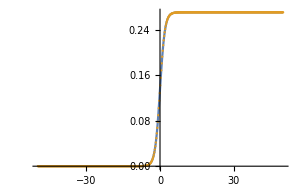
Re
-Graphics-Im
-Graphics-

n=0    s=2    {50.2,1.+0. ⅈ}

Re
-Graphics-Im
-Graphics-

n=1    s=1    {50.2,97.7379458315415046662974559601930032938340080640747840018245528661100131253648595599212313289088811771934825038169016292042452388920142195990388885160300046148771603462225923597574840300465758050223+254.1345606131945111429818043263624162116806193779984844655391804150754697663127105240501637843494349849377342945622852655479269636440190850135764404688446280917300216097251893290635249698889850273693 ⅈ}

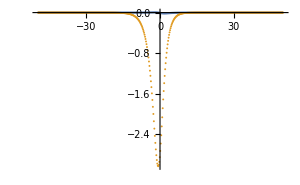
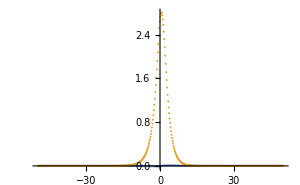
Re
-Graphics-Im
-Graphics-

n=1    s=2    {50.2,0.9965663723937035154139931211994709137477417114053375869626150130782687823325591673939741133429028298543929340347145554251316950862501420775418039980067177571353523482627181207647477666187530936676701+0.000589283008625465885484329384318236287306951172219206344840979166132252530540298791041090108452360440214218376147425434449604329892905265542396453430719264822219954720580166102067935855493592434129 ⅈ}

Re
-Graphics-Im
-Graphics-

n=2    s=1    {-49.8,0.00295015071528932813860581233850122976165719289518577148130805838447638269872606673194028460623749919819958222320828677149782212514482299555376998009208784737043716050692787572614040284217537488285607+0.000056136460011346144695110723386235244113787501758540772055108918361180789041130735479730069120300516050295078553546788814699034731198159617432012168988293283593104909510680577739749548808776562604384 ⅈ}

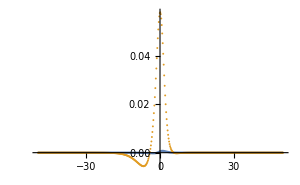
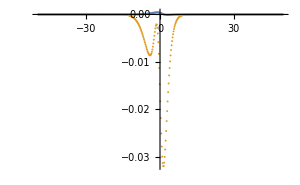
Re
-Graphics-Im
-Graphics-

n=2    s=2    {50.2,0.999999997699444612399471994721375825086461151212419650257981783717304225673967151974027892982312535904984617378036894356647812220558258917038465011162089411333362814018156909994277888804181487181998+1.225976143842084333780691363780307347216043798469828739508223270960069324854522265329644306748666987230892392465856456233686739650625074077499208005404242997955452514242704049884179233904453×10^-9 ⅈ}

Re
-Graphics-Im
-Graphics-

n=3    s=1    {-49.8,0.00076242250902573778910825374937035168364675209061989434705724425606014672562648429012573365952932323441516337067749424173506119722133375791809450528177557812033075848146306523108268699031545937658632+0.00668500449854043910404370467565872340435508402673658719203358646818946553782010078895131667621088383859304892117346852483657612952836878857104703095023068498273338505575740343140028044901565247404401 ⅈ}

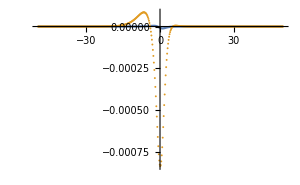
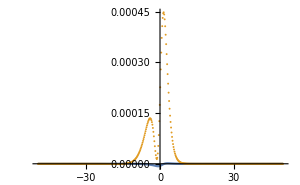
Re
-Graphics-Im
-Graphics-

n=3    s=2    {50.2,0.999999998959539557959043930096502405480509661871502134824140146758927968956120946522233252139378886219619901348762641692276863455114552439455536488747104120040298803867865889644798144481360259922275+5.54265887510066024650802621792652050009010751226682594768376401324913077408191500457513997802894417707686775092448578992471114847066320736875105669294681632766913268888463426349284989303304×10^-10 ⅈ}

Re
-Graphics-Im
-Graphics-

```mathematica
Table[(
Table[(
hoge=Import[StringJoin["lambda1_analytic/k",ToString[k],"_M",ToString[mM],"/210228_lambda1_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;λ1analytic=Table[{xlist[[i]],N[(hoge/.{u->Exp[xlist[[i]]/(2*k)],logu->xlist[[i]]/(2*k)}),prec]},{i,1,nofpoints}];
Reλ1analytic=Table[{xlist[[i]],Re[λ1analytic[[i,2]]]},{i,1,nofpoints}];
Imλ1analytic=Table[{xlist[[i]],Im[λ1analytic[[i,2]]]},{i,1,nofpoints}];
(**)
hoge=Import[StringJoin["lambda1_numerical/k",ToString[k],"_M",ToString[mM],"/210228_lambda1tilde_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],"_xmax",ToString[xmax],"_nofpoints",ToString[nofpoints],".m"]];
λ1numerical=Table[{xlist[[i]],hoge[[i]]/(1+Exp[xlist[[i]]/(4*k)])},{i,1,nofpoints}];
Reλ1numerical=Table[{xlist[[i]],Re[λ1numerical[[i,2]]]},{i,1,nofpoints}];
Imλ1numerical=Table[{xlist[[i]],Im[λ1numerical[[i,2]]]},{i,1,nofpoints}];
(**)
Print["n=",n,"    s=",s,"    ",(Sort[Table[{N[xlist[[i]],3],λ1analytic[[i,2]]/λ1numerical[[i,2]]},{i,1,nofpoints}],Abs[#1[[2]]-1]>Abs[#2[[2]]]&])[[1]]];
range=All;
origin=Automatic;
imsize=300;
Print[Row[{
Column[{"Re",ListPlot[{Reλ1analytic,Reλ1numerical},Joined->{True,False},PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center],Column[{"Im",ListPlot[{Imλ1analytic,Imλ1numerical},Joined->{True,False},PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center]}]];
),{s,1,mM}];
),{n,0,nmax}];
```

## k=2, M=1, n=0~3

### convergence of numerical (ok)

```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=2;
mM=1;
nmax=3;
```

```mathematica
prec=200;
```

```mathematica
xmaxnofpointslist={{50,50},{50,100},{50,200},{50,500}};
```

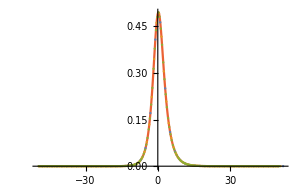
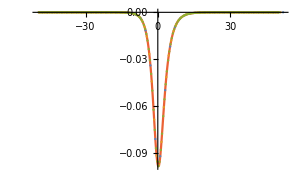
s=1,  n=0
Re
-Graphics-Im
-Graphics-

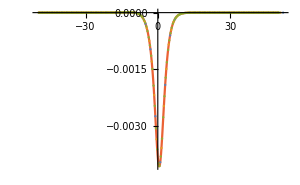
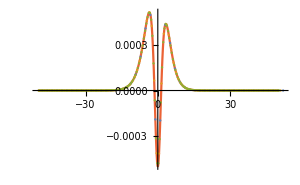
s=1,  n=1
Re
-Graphics-Im
-Graphics-

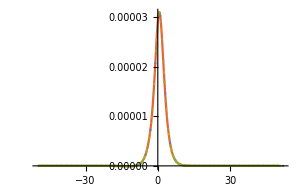
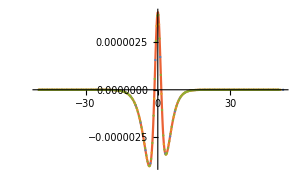
s=1,  n=2
Re
-Graphics-Im
-Graphics-

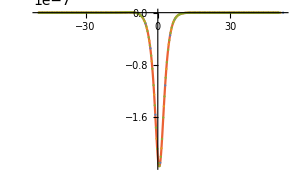
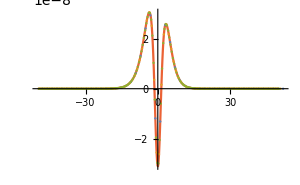
s=1,  n=3
Re
-Graphics-Im
-Graphics-

```mathematica
Table[(
Table[(
Table[(
xmax=xmaxnofpointslist[[a,1]];
nofpoints=xmaxnofpointslist[[a,2]];
(**)
xmin=-xmax;
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[xmin+dx*i,{i,1,nofpoints}];
(**)
hoge=Import[StringJoin["lambda1_numerical/k",ToString[k],"_M",ToString[mM],"/210228_lambda1tilde_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],"_xmax",ToString[xmax],"_nofpoints",ToString[nofpoints],".m"]];
(**)
Reλ1tildenumerical1[a]=Table[{xlist[[i]],Re[hoge[[i]]]},{i,1,nofpoints}];
Imλ1tildenumerical1[a]=Table[{xlist[[i]],Im[hoge[[i]]]},{i,1,nofpoints}];
),{a,1,Length[xmaxnofpointslist]}];
(**)
range=All;
origin=Automatic;
imsize=300;
Print[Column[{
StringJoin["s=",ToString[s],",  n=",ToString[n]],
Row[{Column[{"Re",ListPlot[Table[Reλ1tildenumerical1[a],{a,1,Length[xmaxnofpointslist]}],Joined->Join[ConstantArray[False,Length[xmaxnofpointslist]-1],{True}],PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center],Column[{"Im",ListPlot[Table[Imλ1tildenumerical1[a],{a,1,Length[xmaxnofpointslist]}],Joined->Join[ConstantArray[False,Length[xmaxnofpointslist]-1],{True}],PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center]}]},Center,Frame->True]];
(*
Print["n=",n,"    s=",s,"    ",(Sort[Table[{N[xlist[[i]],3],λ1analytic[[i,2]]/λ1numerical[[i,2]]},{i,1,nofpoints}],Abs[#1[[2]]-1]>Abs[#2[[2]]]&])[[1]]];
*)
),{s,1,mM}];
),{n,0,nmax}];
```

### numerical vs analytic (ok)

```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=2;
mM=1;
nmax=3;
```

```mathematica
xmin=-50;
xmax=50;
nofpoints=500;
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[xmin+dx*i,{i,1,nofpoints}];
prec=200;
```

n=0    s=1    {50.2,1.+0. ⅈ}

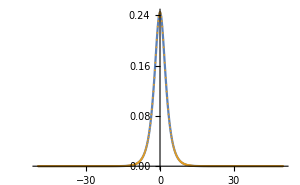
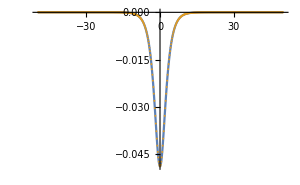
Re
-Graphics-Im
-Graphics-

n=1    s=1    {50.2,0.9999998449960236998986857973662891073224315906187452275021919079972980430799710182650224914264112591865468447113651674735895801508304406597716721832891662494812038057716602329708278476162286963178736+7.993332356752649737679859954045456982077393536263637019861646194047738898249300487208540496450247910652788662670700256948611783387491146649462183600514948987808848773556598005419536816712486×10^-8 ⅈ}

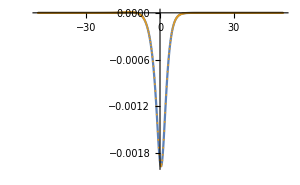
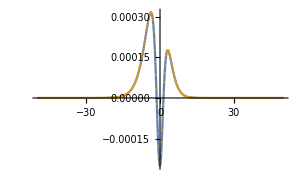
Re
-Graphics-Im
-Graphics-

n=2    s=1    {50.2,0.999999999751693563187182207678705261596763026236807098939552144750598661888493713693627294776044246653836866900509836402171115635605654968252792973006364926514549048853700900895959661046024003077613+2.25422045392796951007026933943309423228165535329093255435125733729781150262029909818987729254928342883698431408220893523800919335384259554826992076265787620579691828173077803032970194345044×10^-10 ⅈ}

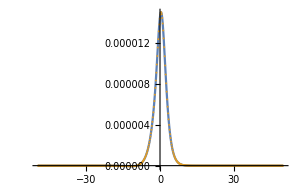
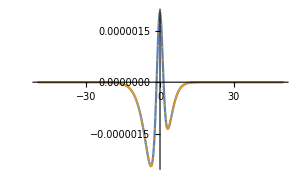
Re
-Graphics-Im
-Graphics-

n=3    s=1    {50.2,0.999999999771723058219588778003666095823490531433913845037547614096360765036630377347294970721308402207393715658086248385270918780080149658919124070826057313630270402366057175570107085178292483356544+2.0634678959356595890365066090695578702973141546212923027881151824482660547123817684269261548346268909708844044774739599772044782555528065044702492140736417918464111261630228427558276507885×10^-10 ⅈ}

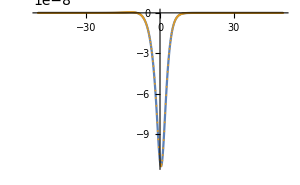
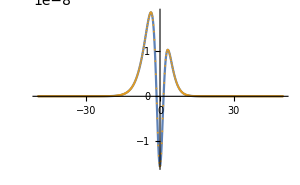
Re
-Graphics-Im
-Graphics-

```mathematica
Table[(
Table[(
hoge=Import[StringJoin["lambda1_analytic/k",ToString[k],"_M",ToString[mM],"/210228_lambda1_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;λ1analytic=Table[{xlist[[i]],N[(hoge/.{u->Exp[xlist[[i]]/(2*k)],logu->xlist[[i]]/(2*k)}),prec]},{i,1,nofpoints}];
Reλ1analytic=Table[{xlist[[i]],Re[λ1analytic[[i,2]]]},{i,1,nofpoints}];
Imλ1analytic=Table[{xlist[[i]],Im[λ1analytic[[i,2]]]},{i,1,nofpoints}];
(**)
hoge=Import[StringJoin["lambda1_numerical/k",ToString[k],"_M",ToString[mM],"/210228_lambda1tilde_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],"_xmax",ToString[xmax],"_nofpoints",ToString[nofpoints],".m"]];
λ1numerical=Table[{xlist[[i]],hoge[[i]]/(1+Exp[xlist[[i]]/(4*k)])},{i,1,nofpoints}];
Reλ1numerical=Table[{xlist[[i]],Re[λ1numerical[[i,2]]]},{i,1,nofpoints}];
Imλ1numerical=Table[{xlist[[i]],Im[λ1numerical[[i,2]]]},{i,1,nofpoints}];
(**)
Print["n=",n,"    s=",s,"    ",(Sort[Table[{N[xlist[[i]],3],λ1analytic[[i,2]]/λ1numerical[[i,2]]},{i,1,nofpoints}],Abs[#1[[2]]-1]>Abs[#2[[2]]]&])[[1]]];
range=All;
origin=Automatic;
imsize=300;
Print[Row[{
Column[{"Re",ListPlot[{Reλ1analytic,Reλ1numerical},Joined->{True,False},PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center],Column[{"Im",ListPlot[{Imλ1analytic,Imλ1numerical},Joined->{True,False},PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center]}]];
),{s,1,mM}];
),{n,0,nmax}];
```

## k=2, M=2, n=0~3

### convergence of numerical (ok)

```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=2;
mM=2;
nmax=3;
```

```mathematica
prec=200;
```

```mathematica
xmaxnofpointslist={{50,50},{50,100},{50,200},{50,500}};
```

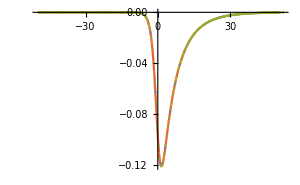
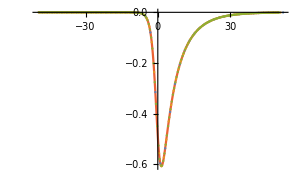
s=1,  n=0
Re
-Graphics-Im
-Graphics-

s=2,  n=0
Re
-Graphics-Im
-Graphics-

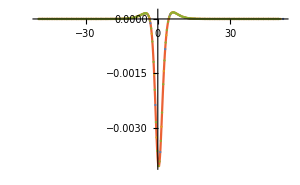
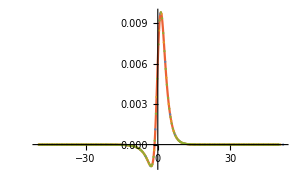
s=1,  n=1
Re
-Graphics-Im
-Graphics-

s=2,  n=1
Re
-Graphics-Im
-Graphics-

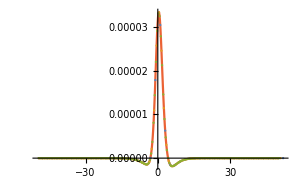
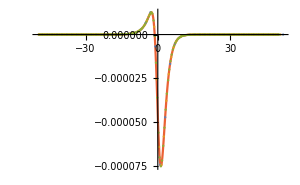
s=1,  n=2
Re
-Graphics-Im
-Graphics-

s=2,  n=2
Re
-Graphics-Im
-Graphics-

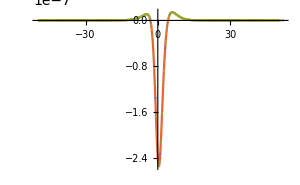
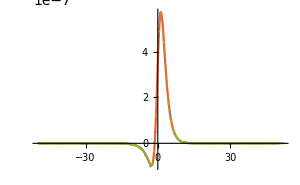
s=1,  n=3
Re
-Graphics-Im
-Graphics-

s=2,  n=3
Re
-Graphics-Im
-Graphics-

```mathematica
Table[(
Table[(
Table[(
xmax=xmaxnofpointslist[[a,1]];
nofpoints=xmaxnofpointslist[[a,2]];
(**)
xmin=-xmax;
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[xmin+dx*i,{i,1,nofpoints}];
(**)
hoge=Import[StringJoin["lambda1_numerical/k",ToString[k],"_M",ToString[mM],"/210228_lambda1tilde_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],"_xmax",ToString[xmax],"_nofpoints",ToString[nofpoints],".m"]];
(**)
Reλ1tildenumerical1[a]=Table[{xlist[[i]],Re[hoge[[i]]]},{i,1,nofpoints}];
Imλ1tildenumerical1[a]=Table[{xlist[[i]],Im[hoge[[i]]]},{i,1,nofpoints}];
),{a,1,Length[xmaxnofpointslist]}];
(**)
range=All;
origin=Automatic;
imsize=300;
Print[Column[{
StringJoin["s=",ToString[s],",  n=",ToString[n]],
Row[{Column[{"Re",ListPlot[Table[Reλ1tildenumerical1[a],{a,1,Length[xmaxnofpointslist]}],Joined->Join[ConstantArray[False,Length[xmaxnofpointslist]-1],{True}],PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center],Column[{"Im",ListPlot[Table[Imλ1tildenumerical1[a],{a,1,Length[xmaxnofpointslist]}],Joined->Join[ConstantArray[False,Length[xmaxnofpointslist]-1],{True}],PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center]}]},Center,Frame->True]];
(*
Print["n=",n,"    s=",s,"    ",(Sort[Table[{N[xlist[[i]],3],λ1analytic[[i,2]]/λ1numerical[[i,2]]},{i,1,nofpoints}],Abs[#1[[2]]-1]>Abs[#2[[2]]]&])[[1]]];
*)
),{s,1,mM}];
),{n,0,nmax}];
```

### numerical vs analytic (ok)

```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=2;
mM=2;
nmax=3;
```

```mathematica
xmin=-50;
xmax=50;
nofpoints=500;
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[xmin+dx*i,{i,1,nofpoints}];
prec=200;
```

n=0    s=1    {50.2,1.+0. ⅈ}

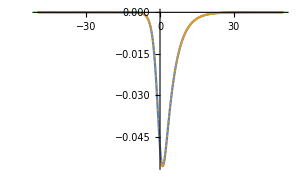
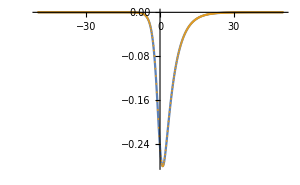
Re
-Graphics-Im
-Graphics-

n=0    s=2    {50.2,1.+0. ⅈ}

Re
-Graphics-Im
-Graphics-

n=1    s=1    {50.2,0.9842310203637137754995638544085449246440454302384572999190924007393547464380302236821656182207022558844970807478913615198540990922200799298784874633658992971989846133566703178197686709069913689238772+0.014168251991170814511430800634800594131398038905558308181134649241078756064120660650804126282238973679206491226910707922475795022785045803140490706760280307140952919028849926711063262279623426081022 ⅈ}

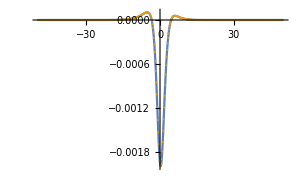
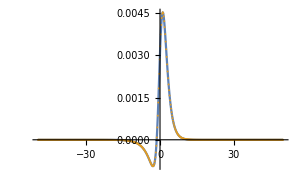
Re
-Graphics-Im
-Graphics-

n=1    s=2    {50.2,0.9999998449960236998986857973662891073224315906187452275021919079972980430799710182650224914264112591865468447113651674735895801508304406597716721832891662494812038057716602329708278476162286963178736+7.993332356752649737679859954045456982077393536263637019861646194047738898249300487208540496450247910652788662670700256948611783387491146649462183600514948987808848773556598005419536816712486×10^-8 ⅈ}

Re
-Graphics-Im
-Graphics-

n=2    s=1    {50.2,0.999968215583725458639875086448986844972204145169459839643041756070179833757076890026686513539438558167527046725634463447289401068686750639910952389025616517635677809446080939503776002904891627187812+0.000079410734234546274099810912542462455901802372748070833315213237653354975721392434463454358067790905725082447767788089012203017907082107415810408382473372489897781867727183176459450773259178265241 ⅈ}

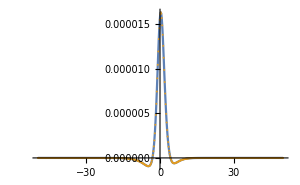
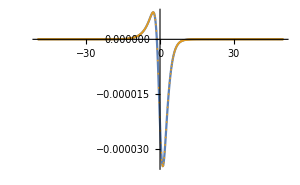
Re
-Graphics-Im
-Graphics-

n=2    s=2    {50.2,0.999999999751693563187182207678705261596763026236807098939552144750598661888493713693627294776044246653836866900509836402171115635605654968252792973006364926514549048853700900895959661046024003077613+2.25422045392796951007026933943309423228165535329093255435125733729781150262029909818987729254928342883698431408220893523800919335384259554826992076265787620579691828173077803032970194345044×10^-10 ⅈ}

Re
-Graphics-Im
-Graphics-

n=3    s=1    {50.2,0.999970809766895971051487012548102924399071747293623580420515549727362979569096466846846348722077253224946787392866948281818367421372674412070967860147756755549931310881298883837589499259649411707164+0.000073584935732212091672090488605368647857871586436184604004008602650755826624237450897507832843724272742184396284597360067583049680472999066194171932485574241959717750940230553102129850138039513488 ⅈ}

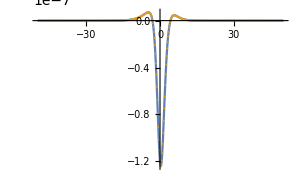
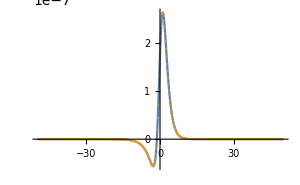
Re
-Graphics-Im
-Graphics-

n=3    s=2    {50.2,0.999999999771723058219588778003666095823490531433913845037547614096360765036630377347294970721308402207393715658086248385270918780080149658919124070826057313630270402366057175570107085178292483356544+2.0634678959356595890365066090695578702973141546212923027881151824482660547123817684269261548346268909708844044774739599772044782555528065044702492140736417918464111261630228427558276507885×10^-10 ⅈ}

Re
-Graphics-Im
-Graphics-

```mathematica
Table[(
Table[(
hoge=Import[StringJoin["lambda1_analytic/k",ToString[k],"_M",ToString[mM],"/210228_lambda1_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],".m"]]//ComplexExpand//TrigReduce;λ1analytic=Table[{xlist[[i]],N[(hoge/.{u->Exp[xlist[[i]]/(2*k)],logu->xlist[[i]]/(2*k)}),prec]},{i,1,nofpoints}];
Reλ1analytic=Table[{xlist[[i]],Re[λ1analytic[[i,2]]]},{i,1,nofpoints}];
Imλ1analytic=Table[{xlist[[i]],Im[λ1analytic[[i,2]]]},{i,1,nofpoints}];
(**)
hoge=Import[StringJoin["lambda1_numerical/k",ToString[k],"_M",ToString[mM],"/210228_lambda1tilde_k",ToString[k],"_M",ToString[mM],"_s",ToString[s],"_n",ToString[n],"_xmax",ToString[xmax],"_nofpoints",ToString[nofpoints],".m"]];
λ1numerical=Table[{xlist[[i]],hoge[[i]]/(1+Exp[xlist[[i]]/(4*k)])},{i,1,nofpoints}];
Reλ1numerical=Table[{xlist[[i]],Re[λ1numerical[[i,2]]]},{i,1,nofpoints}];
Imλ1numerical=Table[{xlist[[i]],Im[λ1numerical[[i,2]]]},{i,1,nofpoints}];
(**)
Print["n=",n,"    s=",s,"    ",(Sort[Table[{N[xlist[[i]],3],λ1analytic[[i,2]]/λ1numerical[[i,2]]},{i,1,nofpoints}],Abs[#1[[2]]-1]>Abs[#2[[2]]]&])[[1]]];
range=All;
origin=Automatic;
imsize=300;
Print[Row[{
Column[{"Re",ListPlot[{Reλ1analytic,Reλ1numerical},Joined->{True,False},PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center],Column[{"Im",ListPlot[{Imλ1analytic,Imλ1numerical},Joined->{True,False},PlotRange->range,AxesOrigin->origin,ImageSize->imsize]},Center]}]];
),{s,1,mM}];
),{n,0,nmax}];
```